# MODUŁ 2

## 1. Zaimplementuj Proste Przeszukiwanie Lokalne (Local Search) (dla funkcji co najmniej 2 zmiennych).

```mathematica
localSearch[f_,xmin_,xmax_,ymin_,ymax_,numTrials_,e_,numberOfPoints_,randomPoint_]:=Module[{startPoints,bestPoint,bestValue,neighborhood={},results={},locations={},sum,actualValue,actualPoint,means={}},
(*wybór losowego rozwiązania początkowego, które będzie też najlepszym punktem na samym początku, w podanym zakresie za pomocą funkcji i określenie jego jakości *)
bestPoint=randomPoint;
bestValue=f[bestPoint⟦1⟧,bestPoint⟦2⟧];

For[i=1,i≤numTrials,i++,
sum=0;
(* generowanie punktów w danym sąsiedztwie -> obszar kwadratu, wokół najlepszego punktu *)
neighborhood=RandomPoint[Rectangle[bestPoint-e,bestPoint+e],numberOfPoints];

For[j=1,j≤Length[neighborhood],j++,
(* bieżący punkt to kolejny punkt z wygenerowanych w sąsiedztwie punktów *)
actualPoint=neighborhood⟦j⟧;
(* obliczanie wartości dla bieżącego punktu *)
actualValue=f[actualPoint⟦1⟧,actualPoint⟦2⟧];
(* sumowanie wszystkich wyników w danej iteracji *)
sum=sum+actualValue;

(* jeśli wartość bieżącego punktu jest mniejsza od najlepszego wyniku, to przypisujemy do niego bieżącą wartość oraz do najlepszego punktu bieżący punkt*)
If[actualValue< bestValue,bestValue=actualValue;bestPoint=actualPoint;];

];
(* dodanie wszystkich potrzebnych wartości do wykresów do list*)
AppendTo[locations,bestPoint];
AppendTo[results,bestValue];
AppendTo[means, sum/numberOfPoints];
];
(*zwracanie wyniku*)
Return[{bestPoint,bestValue ,results,means,locations,f,xmin,xmax,ymin,ymax,numTrials }];
;]
```

## 2. Przetestuj procedury na funkcjach testowych (zgodnie z zasadami omawianymi w module 1) nie zapominając o funkcjach wielomodalnych. Porównaj i zinterpretuj wyniki.

```mathematica
dzialanieHeurystyki2[algorithm_]:=Module[{bestPointOverall,bestValueOverall,results,means,locations,animation,optimum,resultsPlot,meansPlot,xmin,xmax,ymin,ymax,function,iterations},
{bestPointOverall,bestValueOverall,results,means,locations,function,xmin,xmax,ymin,ymax,iterations}=algorithm;

(* znalezione optimum\small{x_{max}} oraz wartość funkcji celu w tym punkcie*)
optimum=StringJoin["fMin(",ToString[bestPointOverall⟦1⟧],", ",ToString[bestPointOverall⟦2⟧],")=",ToString[bestValueOverall]];

(* przebieg wartości optymalnej w kolejnych iteracjach\small{x_{best,i}} *)
resultsPlot=ListPlot[results,PlotStyle->{Purple},AxesLabel->{"ilość iteracji","wartość"}, PlotLabel->"przebieg Φ(xBest)",ImageSize->400 ];

(* przebieg wartości średniej (w populacji) w kolejnych iteracjach\small{x_{av,i}} *)
meansPlot=ListLinePlot[means,PlotStyle->{Purple,Thick},AxesLabel->{"ilość iteracji","średnia wartość"},PlotLabel->"przebieg Φ średnie w iteracji" ,ImageSize->400];
(* ruch punktu\small{x_{best,i}} na płaszczyźnie (dla problemów 2D) *)
animation=Animate[Module[{currentLocation=locations⟦j⟧,from=locations⟦1;;j-1⟧,to=locations[[2;;j]]},DensityPlot[function[x,y],{x,xmin,xmax},{y,ymin,ymax},Epilog->{Red,PointSize[Large],Point[currentLocation],Thick,Line[Transpose[{from,to}]],Thin,Line[Transpose[{locations⟦1;;j-1⟧,locations⟦2;;j⟧}]]}]],{j,1,iterations,1}];
Print[Grid[{{optimum,resultsPlot},{meansPlot,animation}},Frame->All,Alignment->Left,ItemSize->{36,25}]];
]
```

-> funkcja sferyczna

```mathematica
SphericFunction2D[x_,y_]:=x^2+y^2;
```

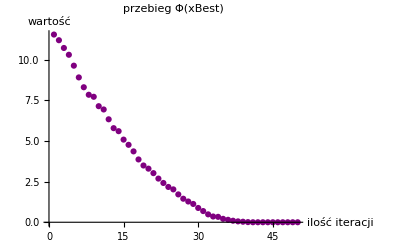
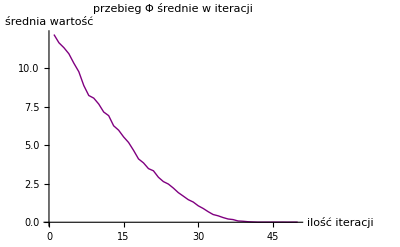
fMin(-0.000422447, -0.00363207)=0.0000133704 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[SphericFunction2D, -5,5,-5,5,50,0.1,10,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

Algorytm bez problemu znajduje minimum globalne.

-> funkcja Rastringa

```mathematica
RastriginFunction2D[x_,y_]:=x^2-Cos[18*x]+y^2-Cos[18*y];
```

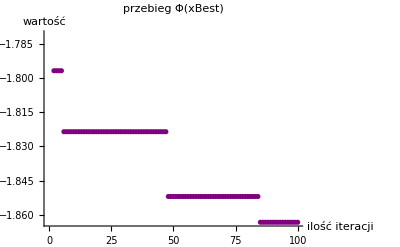
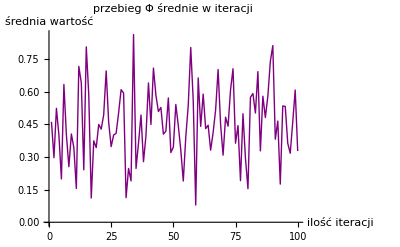
fMin(0.337167, -0.00108578)=-1.86328 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[RastriginFunction2D, -1,1,-1,1,100,0.3,30,{RandomReal[{-1,1}],RandomReal[{-1,1}]}]]
```

Algorytm zazwyczaj dobrze radzi sobie ze znalezieniem minimum globalnego.

-> funkcja Ackley’a

```mathematica
AckleyFunction2D[x_,y_]:=-20*Exp[-0.2*√(1/2*(x^2+y^2))]-Exp[1/2*(Cos[2*Pi*x]+Cos[2*Pi*y])]+20+ⅇ;
```

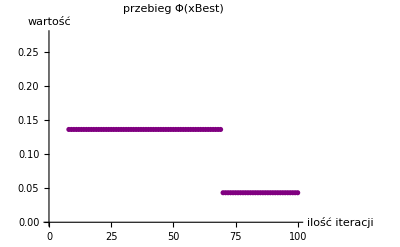
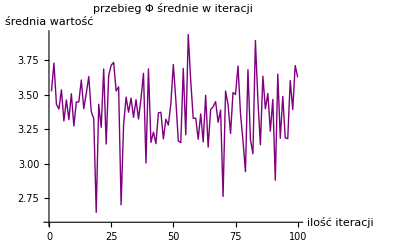
fMin(0.0133527, -0.00243501)=0.0432883 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[AckleyFunction2D, -5,5,-5,5,100,0.8,20,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

Obszar generowania sąsiedztwa jest duży, gdyż inaczej algorytm utykał w minimach lokalnych.

->dolina Rosenbrocka

```mathematica
RosenbrockFunction2D[x_,y_]:=(1-x)^2+100(y-x^2)^2;
```

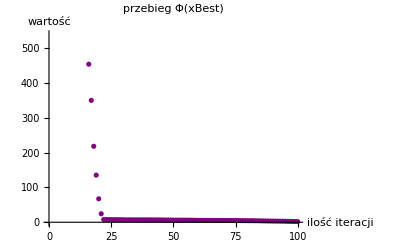
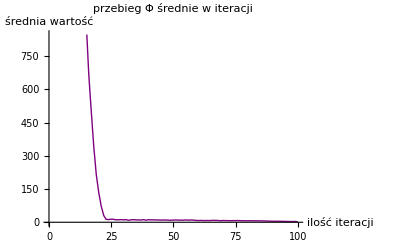
fMin(-0.321106, 0.0965558)=1.74962 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[RosenbrockFunction2D, -10,10,-10,10,100,0.1,20,{RandomReal[{-10,10}],RandomReal[{-10,10}]}]]
```

W zależności, gdzie zostanie wygenerowany punkt początkowy, algorytm radzi sobie lepiej i gorzej.

-> funkcja Himmelblaua

```mathematica
HimmelblauFunction2D[x_,y_]:=(x^2+y-11)^2+(x+y^2-7)^2;
```

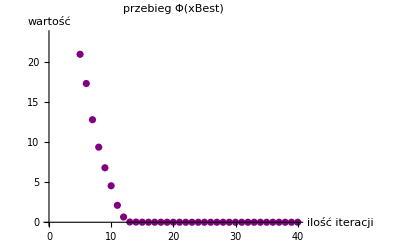
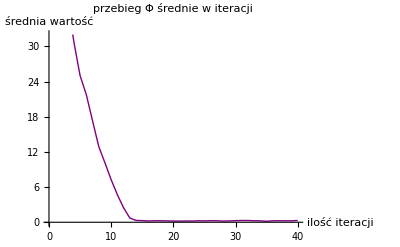
fMin(-2.81097, 3.12501)=0.00275544 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[HimmelblauFunction2D, -5,5,-5,5,40,0.1,20,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

Bez problemu znajduje jedno z minimów globalnych.

->funkcja Beale’a

```mathematica
BealeFunction2D[x_,y_]:=(1.5-x+x*y)^2+(2.25-x+x*y^2)^2+(2.625-x+x y^3)^2;
```

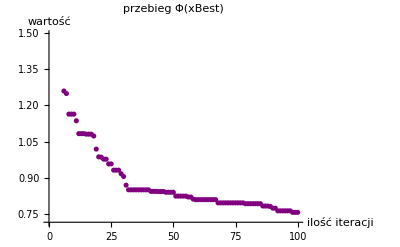
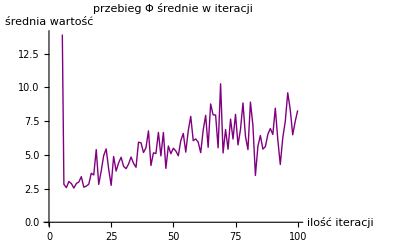
fMin(-4.58608, 1.18444)=0.757317 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[localSearch[BealeFunction2D, -4.5,4.5,-4.5,4.5,100,0.2,20,{RandomReal[{-4.5,4.5}],RandomReal[{-4.5,4.5}]}]]
```

Jeżeli wygenerowany początkowy punkt jest blisko lokalnego minimum wtedy zazwyczaj tam utyka i nie znajduje minimum globalnego.

Algorytm zazwyczaj radził sobie bardzo dobrze z powyższymi funkcjami testowymi. Najgorsze wyniki były przy funkcji Beale’a, gdyż jak wpadał do minimum lokalnego, to PPL tam utykał. Również z doliną Rosenbrocka radził sobie średnio, ale to wszystko zależy gdzie wygenerował się punkt początkowy. Dla reszty funkcji z wybranymi parametrami algorytm bez problemu znajdował minimum globalne.
W zależności od podanych przez nas parametrów, algorytm będzie sobie radził lepiej lub gorzej dla danych funkcji testowych.

## 3. Rozbuduj PPL do przeszukiwania ze zmiennym sąsiedztwem.

```mathematica
neighborhoodSearch[f_,xmin_,xmax_,ymin_,ymax_,e_, kMax_,randomPoint_]:=Module[{startPoints,bestPoint,bestValue,neighborhood={},results={},locations={},sum,actualValue,actualPoint,means={},k,iterations=0},
(*wybór losowego rozwiązania początkowego, które będzie też najlepszym punktem na samym początku, w podanym zakresie za pomocą funkcji i określenie jego jakości *)
bestPoint=randomPoint;
bestValue=f[bestPoint⟦1⟧,bestPoint⟦2⟧];

k=1;
While[k≤ kMax,
sum=0;
(* generowanie punktów w danym sąsiedztwie -> obszar kwadratu, wokół najlepszego punktu *)
neighborhood=RandomPoint[Rectangle[bestPoint-e,bestPoint+e],k];
For[j=1,j≤Length[neighborhood],j++,
(* bieżący punkt to kolejny punkt wygenerowany w sąsiedztwie *)
actualPoint=neighborhood⟦j⟧;
(* obliczanie wartości dla bieżącego punktu *)
actualValue=f[actualPoint⟦1⟧,actualPoint⟦2⟧];
sum=sum+actualValue;
(* jeśli wartość bieżącego punktu jest mniejsza od najlepszego wyniku, to przypisujemy do niego bieżącą wartość oraz do najlepszego punktu bieżący punkt oraz ilość generowanych punktów w sąsiedztwie ustawiamy na 1, w przeciwnym wypadku zwiększamy ilość punktów w sąsiedztwie o 1*)
If[actualValue< bestValue,bestValue=actualValue;bestPoint=actualPoint;k=1,k++];

];
(* dodanie wszystkich potrzebnych wartości do wykresów do list*)
AppendTo[locations,bestPoint];
AppendTo[results,bestValue];
AppendTo[means, sum/Length[neighborhood]];
iterations++
];
(*zwracanie wyniku*)
Return[{bestPoint,bestValue ,results,means,locations,f,xmin,xmax,ymin,ymax,iterations}];

];
```

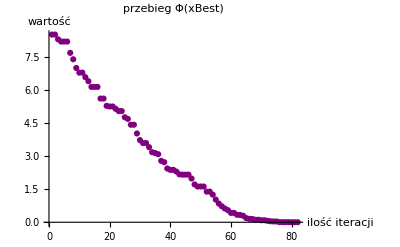
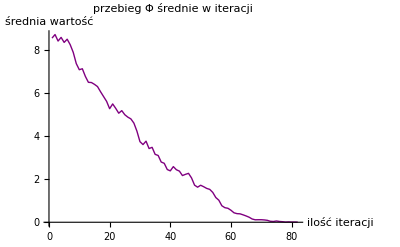
fMin(0.0280853, 0.0172287)=0.00108561 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[SphericFunction2D, -5,5,-5,5,0.1,20,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

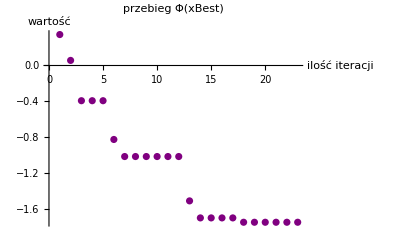
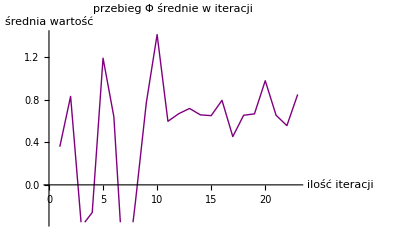
fMin(0.349907, 0.339228)=-1.74674 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[RastriginFunction2D, -1,1,-1,1,0.25,100,{RandomReal[{-1,1}],RandomReal[{-1,1}]}]]
```

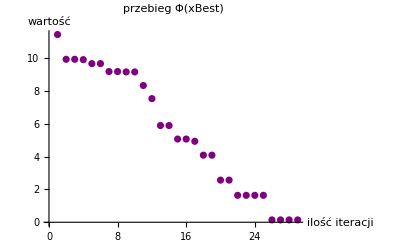
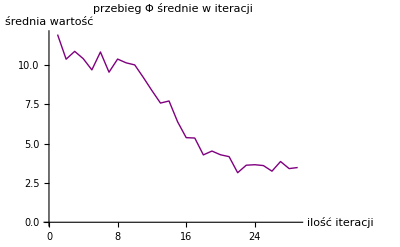
fMin(0.0374296, 0.0027252)=0.143219 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[AckleyFunction2D, -5,5,-5,5,0.8,100,
{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

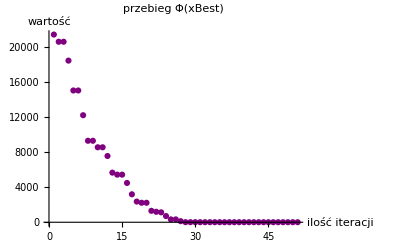
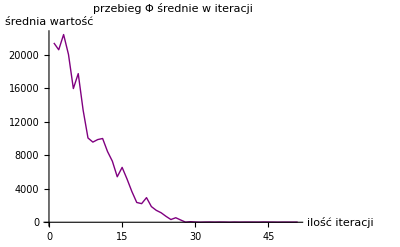
fMin(-1.47317, 2.19243)=6.16585 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[RosenbrockFunction2D, -5,5,-5,5,0.2,40,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

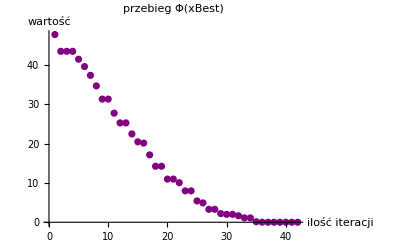
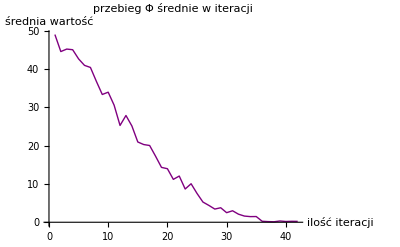
fMin(-2.79937, 3.13597)=0.00197759 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[HimmelblauFunction2D, -5,5,-5,5,0.1,20,{RandomReal[{-5,5}],RandomReal[{-5,5}]}]]
```

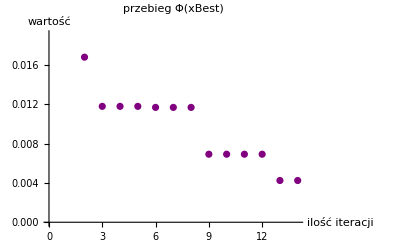
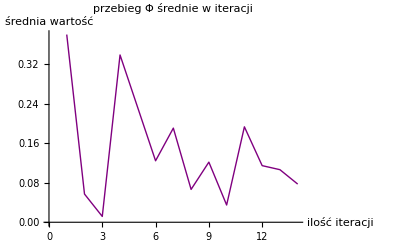
fMin(3.1791, 0.54071)=0.00424517 | -Graphics-
-Graphics- |

```mathematica
dzialanieHeurystyki2[neighborhoodSearch[BealeFunction2D, -4.5,4.5,-4.5,4.5,0.1,20,{RandomReal[{-4.5,4.5}],RandomReal[{-4.5,4.5}]}]]
```

## 4. Porównaj działanie metod obu zaimplementowanych metod.

```mathematica
resultComparison[algorithm1_,algorithm2_,functionName_,min_,numTrials_]:=Module[{bestValues1=0,bestValues2=0,mean1=0,mean2=0},

For[i=1,i≤numTrials,i++,
bestValues1=bestValues1+algorithm1[[2]];
bestValues2=bestValues2+algorithm2[[2]];
];

mean1=bestValues1/numTrials;
mean2=bestValues2/numTrials;
Print[StringJoin["Wynik prostego przeszukiwania lokalnego: ",ToString[mean1]]];
Print[StringJoin["Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: ",ToString[mean2]]];
If[Abs[mean1-min]<Abs[mean2-min], Print[StringJoin["Proste przeszukiwanie lokalne okazało się lepsze dla funkcji ",functionName]],Print[StringJoin["Przeszukiwanie lokalne ze zmiennym sasiedztwem okazało się lepsze dla funkcji ",functionName]]];

];
```

->funkcja sferyczna

```mathematica
x1={RandomReal[{-5,5}],RandomReal[{-5,5}]};
resultComparison[localSearch[SphericFunction2D, -5,5,-5,5,50,0.1,10,x1],neighborhoodSearch[SphericFunction2D, -5,5,-5,5,0.1,20,x1],"sferycznej",0,1000]
```

Wynik prostego przeszukiwania lokalnego: 0.0000772057

Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: 0.000553896

Proste przeszukiwanie lokalne okazało się lepsze dla funkcji sferycznej

Oba algorytmy dają bardzo zbliżone wyniki jednak zazwyczaj proste przeszukiwanie lokalne radzi sobie lepiej, gdy liczba iteracji =100 i więcej. Przy mniejszej ilości powtórzeń algorytmy się wymieniają w tym, który jest lepszy.

-> funkcja Rastrigina

```mathematica
x2={RandomReal[{-1,1}],RandomReal[{-1,1}]};
resultComparison[localSearch[RastriginFunction2D, -1,1,-1,1,50,0.1,20,x2],neighborhoodSearch[RastriginFunction2D, -1,1,-1,1,0.1,20,x2],"Rastrigina",-2,1000]
```

Wynik prostego przeszukiwania lokalnego: -1.87758

Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: -1.36468

Proste przeszukiwanie lokalne okazało się lepsze dla funkcji Rastrigina

Oba algorytmy dają bardzo zbliżone wyniki jednak zazwyczaj proste przeszukiwanie lokalne radzi sobie lepiej.

-> funkcja Ackley’a

```mathematica
x3={RandomReal[{-5,5}],RandomReal[{-5,5}]};
resultComparison[localSearch[AckleyFunction2D, -5,5,-5,5,100,0.9,20,x3],neighborhoodSearch[AckleyFunction2D, -5,5,-5,5,0.9,20,x3],"Ackley'a",0,1000]
```

Wynik prostego przeszukiwania lokalnego: 0.0574346

Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: 0.474128

Proste przeszukiwanie lokalne okazało się lepsze dla funkcji Ackley'a

Dla mniejszego obszaru sąsiedztwa częściej lepiej sobie radzi przeszukiwanie lokalne ze zmiennym sąsiedztwem, natomiast, gdy ten obszar (e) zwiększamy, częściej bliższe wyniki osiąga proste przeszukiwanie lokalne.

->  dolina Rosenbrocka

```mathematica
x4={RandomReal[{-10,10}],RandomReal[{-10,10}]};
resultComparison[localSearch[RosenbrockFunction2D, -10,10,-10,10,50,0.3,60,x4],neighborhoodSearch[RosenbrockFunction2D, -10,10,-10,10,0.3,30,x4],"Rosenbrocka",0,1000]
```

Wynik prostego przeszukiwania lokalnego: 0.000108166

Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: 0.00156913

Proste przeszukiwanie lokalne okazało się lepsze dla funkcji Rosenbrocka

Proste przeszukiwanie lokalne zazwyczaj osiąga lepsze wyniki.

-> funkcja Beale’a

```mathematica
x5={RandomReal[{-4.5,4.5}],RandomReal[{-4.5,4.5}]};
resultComparison[localSearch[BealeFunction2D, -4.5,4.5,-4.5,4.5,50,0.1,20,x5],neighborhoodSearch[BealeFunction2D, -4.5,4.5,-4.5,4.5,0.1,40,x5],"Beale'a",0,1000]
```

Wynik prostego przeszukiwania lokalnego: 1.43578

Wynik przeszukiwania lokalnego ze zmiennym sasiedztwem: 3.76159

Proste przeszukiwanie lokalne okazało się lepsze dla funkcji Beale'a

Im wyższa ilość iteracji w prostym przeszukiwaniu lokalnym, tym lepszy wynik, analogicznie w przypadku przeszukiwania lokalnego ze zmiennym sąsiedztwem ale dla ilości generowanych punktów w sąsiedztwie.  Jednakże w moich przeprowadzonych testach częściej trochę lepiej radziło sobie PPL, ale wyniki zazwyczaj były bardzo zbliżone.